```mathematica
(*Directory[]*)
```

```mathematica
dir1="C:\\Users\\mariana\\Desktop\\LastPictures\\Reactive\\5%\\6M\\AveragePicture\\";
```

```mathematica
SetDirectory[dir1];
```

```mathematica
list=FileNames["*.jpg"];
```

```mathematica
tfinal=Length[list];
```

```mathematica
For[time=1,time<tfinal+1,time=time+1,
Prin[time];
file=dir1<>"data"<>ToString[time]<>".jpg";
img=Import[file];
imgDRBinary=Binarize[img,0.004];
imgc=CommonestFilter[imgDRBinary,20];
imgDRBinary=ImageMultiply[imgDRBinary,imgc];
databn=ImageData[imgDRBinary];
(*Print[FindThreshold[img]];*)
(*Print[imgDRBinary];*)
img=ImageMultiply[img,imgc];
{r,g,b}=ColorSeparate[img];
{w,h}=ImageDimensions[img];
data=ImageData[r,"Byte"];
datag=ImageData[g,"Byte"];
datab=ImageData[b,"Byte"];

Print[time];
(*Radius of the thermal as a function of the vertical distance, b*)
rb[time]=Total[databn,{2}]/2;
bRed[time]=Total[data,{2}];
bGreen[time]=Total[datag,{2}];
bBlue[time]=Total[datab,{2}];
rbc[time]=rb[time]/.{0->10^8};
cbRed[time]=bRed[time]/(2*rbc[time]);
cbGreen[time]=bGreen[time]/(2*rbc[time]);
cbBlue[time]=bBlue[time]/(2*rbc[time]);


ClearAll[radius];
(*Radius of the thermal as a function of the horizontal distance, a*)
Print[MemoryInUse[],"    ",MaxMemoryUsed[]];

ra[time]=Total[databn]/2;
aRed[time]=Total[data];
aGreen[time]=Total[datag];
aBlue[time]=Total[datab];
rac[time]=ra[time]/.{0->10^8};
caRed[time]=aRed[time]/(2*rac[time]);
caGreen[time]=aGreen[time]/(2*rac[time]);
caBlue[time]=aBlue[time]/(2*rac[time]);

ClearAll[data,databn,datag,datab,r,g,b,img1,imgDRBinary,img,radius];
 ]
```

1

183487524    183923668

2

184102060    184536164

3

184488692    184919924

4

184923580    185351588

5

185404140    185828868

6

185926196    186347100

7

186484996    186903700

8

187074852    187491652

9

187683860    188098532

10

188228956    188650340

11

188745876    189168204

12

189231356    189658524

13

189670060    190095700

14

190019148    190451836

15

190289780    190726340

16

190493884    190933388

17

190671868    191111380

18

190852884    191292724

19

191033796    191473340

20

191217044    191656588

21

191400244    191839788

22

191583108    192022652

23

191766500    192206044

24

191949532    192389076

25

192132884    192572428

26

192315988    192755532

27

192499044    192938588

28

192682244    193121788

29

192865412    193304956

30

193048300    193487844

31

193231556    193671100

32

193414820    193854364

33

193598060    194037604

34

193781188    194220732

```mathematica
{lr,lR,lG,lB,lcR,lcG,lcB}={Manipulate[ListPlot[rb[time],PlotRange->All, AxesLabel->{"y (pixel)","b(pixel)"}],{time,1,tfinal,1,Appearance->"Labeled"}],Manipulate[ListPlot[bRed[time],PlotRange->All, AxesLabel->{"y (pixel)","(∑R)_(x=1)^w (Bytes)"}],{time,1,tfinal,1,Appearance->"Labeled"}],Manipulate[ListPlot[bGreen[time],PlotRange->All, AxesLabel->{"y (pixel)","(∑G)_(x=1)^w (Bytes)"}],{time,1,tfinal,1,Appearance->"Labeled"}],Manipulate[ListPlot[bBlue[time],PlotRange->All, AxesLabel->{"y (pixel)","(∑B)_(x=1)^w (Bytes)"}],{time,1,tfinal,1,Appearance->"Labeled"}],Manipulate[ListPlot[cbRed[time],PlotRange->All, AxesLabel->{"y (pixel)","(∑R/b)_(x=1)^w (Bytes)"}],{time,1,tfinal,1,Appearance->"Labeled"}],Manipulate[ListPlot[cbGreen[time],PlotRange->All, AxesLabel->{"y (pixel)","(∑G/b)_(x=1)^w (Bytes)"}],{time,1,tfinal,1,Appearance->"Labeled"}],Manipulate[ListPlot[cbBlue[time],PlotRange->All, AxesLabel->{"y (pixel)","(∑B/b)_(x=1)^w (Bytes)"}],{time,1,tfinal,1,Appearance->"Labeled"}]}
```

{,,,,,,}

ListPlot::lpn: rb[1] is not a list of numbers or pairs of numbers.

ListPlot::lpn: bRed[1] is not a list of numbers or pairs of numbers.

ListPlot::lpn: bGreen[1] is not a list of numbers or pairs of numbers.

ListPlot::lpn: bBlue[1] is not a list of numbers or pairs of numbers.

ListPlot::lpn: cbRed[1] is not a list of numbers or pairs of numbers.

ListPlot::lpn: cbGreen[1] is not a list of numbers or pairs of numbers.

ListPlot::lpn: cbBlue[1] is not a list of numbers or pairs of numbers.

```mathematica
{cr,cR,cG,cB,ccR,ccG,ccB}={Manipulate[ListPlot[ra[time],PlotRange->All, AxesLabel->{"x (pixel)","b(pixel)"}],{time,1,tfinal,1,Appearance->"Labeled"}],Manipulate[ListPlot[aRed[time],PlotRange->All, AxesLabel->{"x (pixel)","(∑R)_(x=1)^w (Bytes)"}],{time,1,tfinal,1,Appearance->"Labeled"}],Manipulate[ListPlot[aGreen[time],PlotRange->All, AxesLabel->{"x (pixel)","(∑G)_(x=1)^w (Bytes)"}],{time,1,tfinal,1,Appearance->"Labeled"}],Manipulate[ListPlot[aBlue[time],PlotRange->All, AxesLabel->{"x (pixel)","(∑B)_(x=1)^w (Bytes)"}],{time,1,tfinal,1,Appearance->"Labeled"}],Manipulate[ListPlot[caRed[time],PlotRange->All, AxesLabel->{"x (pixel)","(∑R/a)_(x=1)^w (Bytes)"}],{time,1,tfinal,1,Appearance->"Labeled"}],Manipulate[ListPlot[caGreen[time],PlotRange->All, AxesLabel->{"x (pixel)","(∑G/a)_(x=1)^w (Bytes)"}],{time,1,tfinal,1,Appearance->"Labeled"}],Manipulate[ListPlot[caBlue[time],PlotRange->All, AxesLabel->{"x (pixel)","(∑B/a)_(x=1)^w (Bytes)"}],{time,1,tfinal,1,Appearance->"Labeled"}]}
```

{,,,,,,}

ListPlot::lpn: ra[1] is not a list of numbers or pairs of numbers.

ListPlot::lpn: aRed[1] is not a list of numbers or pairs of numbers.

ListPlot::lpn: aGreen[1] is not a list of numbers or pairs of numbers.

ListPlot::lpn: aBlue[1] is not a list of numbers or pairs of numbers.

ListPlot::lpn: caRed[1] is not a list of numbers or pairs of numbers.

ListPlot::lpn: caGreen[1] is not a list of numbers or pairs of numbers.

ListPlot::lpn: caBlue[1] is not a list of numbers or pairs of numbers.

```mathematica
For[time=1,time<tfinal+1,time=time+1,

rbf=Position[rb[time],_?(#>10&)];
fpt[time]=Max[rbf];
fp[time]=fpt[time]/.{-∞->0};

maxb[time]=Max[rb[time]];
Area[time]=Total[rb[time]]*2;
TotalRed[time]=Total[bRed[time]];
TotalGreen[time]=Total[bGreen[time]];
TotalBlue[time]=Total[bBlue[time]];
Print[Area[time]];
Areac[time]=Area[time]/.{0->10^8};
Print[Areac[time]];
cRed[time]=TotalRed[time]/Areac[time];
cGreen[time]=TotalGreen[time]/Areac[time];
cBlue[time]=TotalBlue[time]/Areac[time];

];
```

31555

31555

102831

102831

178040

178040

258494

258494

341276

341276

421351

421351

498848

498848

561908

561908

569322

569322

528518

528518

457422

457422

337099

337099

142019

142019

36066

36066

5423

5423

0

100000000

0

100000000

0

100000000

0

100000000

0

100000000

0

100000000

0

100000000

0

100000000

0

100000000

0

100000000

0

100000000

0

100000000

0

100000000

0

100000000

0

100000000

0

100000000

0

100000000

0

100000000

0

100000000

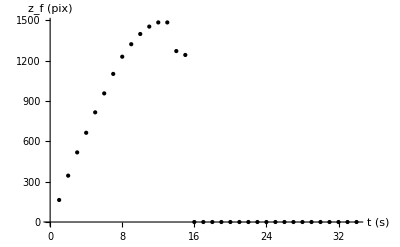
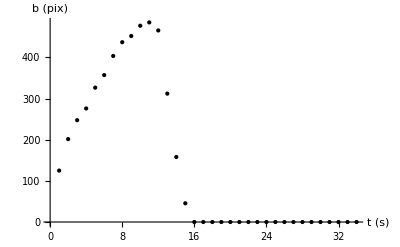
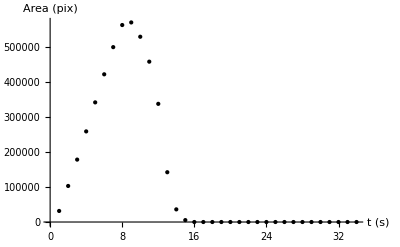
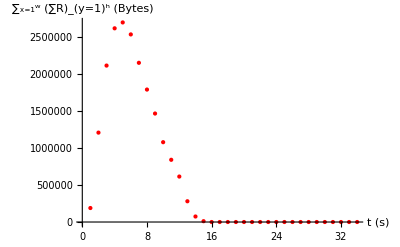
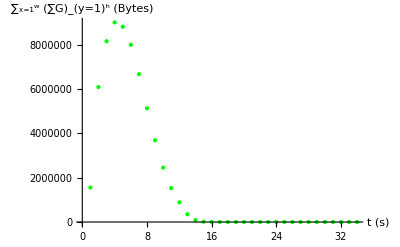
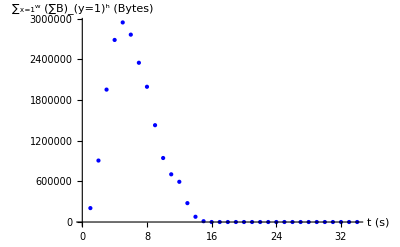
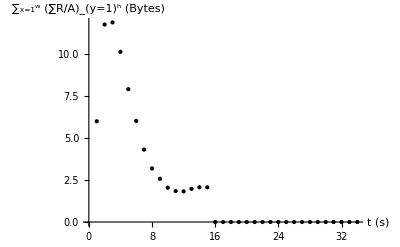
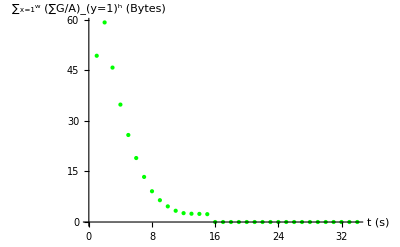

```mathematica
{frontposition, radiust, areat, redt, greent, bluet,cRedt,cGreent,cBluet}=
{ListPlot[Table[fp[time],{time,1,tfinal}], AxesLabel->{"t (s)","z_f (pix)"}, PlotStyle->Black],ListPlot[Table[maxb[time],{time,1,tfinal}], AxesLabel->{"t (s)","b (pix)"}, PlotStyle->Black],ListPlot[Table[Area[time],{time,1,tfinal}], AxesLabel->{"t (s)","Area (pix)"}, PlotStyle->Black],ListPlot[Table[TotalRed[time],{time,1,tfinal}], AxesLabel->{"t (s)","∑_(x=1)^w (∑R)_(y=1)^h (Bytes)"}, PlotStyle->Red],ListPlot[Table[TotalGreen[time],{time,1,tfinal}], AxesLabel->{"t (s)","∑_(x=1)^w (∑G)_(y=1)^h (Bytes)"}, PlotStyle->Green],ListPlot[Table[TotalBlue[time],{time,1,tfinal}], AxesLabel->{"t (s)","∑_(x=1)^w (∑B)_(y=1)^h (Bytes)"}, PlotStyle->Blue],ListPlot[Table[cRed[time],{time,1,tfinal}], AxesLabel->{"t (s)","∑_(x=1)^w (∑R/A)_(y=1)^h (Bytes)"}, PlotStyle->Black],ListPlot[Table[cGreen[time],{time,1,tfinal}], AxesLabel->{"t (s)","∑_(x=1)^w (∑G/A)_(y=1)^h (Bytes)"}, PlotStyle->Green],ListPlot[Table[cBlue[time],{time,1,tfinal}], AxesLabel->{"t (s)","∑_(x=1)^w (∑B/A)_(y=1)^h (Bytes)"}, PlotStyle->Blue]}
```